# Hilbert Matrix

## Basic Examples

3x3 Hilbert matrix:

```mathematica
HilbertMatrix[3]//MatrixForm
```

(1 | 1/2 | 1/3
1/2 | 1/3 | 1/4
1/3 | 1/4 | 1/5)

3x5 Hilbert matrix:

```mathematica
HilbertMatrix[{3,5}]//MatrixForm
```

(1 | 1/2 | 1/3 | 1/4 | 1/5
1/2 | 1/3 | 1/4 | 1/5 | 1/6
1/3 | 1/4 | 1/5 | 1/6 | 1/7)

## Options

### WorkingPrecision

A Hilbert matrix with machine-number entries:

```mathematica
HilbertMatrix[3,WorkingPrecision->MachinePrecision]
```

{{1.,0.5,0.333333},{0.5,0.333333,0.25},{0.333333,0.25,0.2}}

A Hilbert matrix with 24-digit precision entries:

```mathematica
HilbertMatrix[3,WorkingPrecision->24]
```

{{1.,0.5,0.333333333333333333333333},{0.5,0.333333333333333333333333,0.25},{0.333333333333333333333333,0.25,0.2}}

## Properties & Relations

Square Hilbert matrices are real symmetric:

```mathematica
h=HilbertMatrix[RandomInteger[{1,99}]];
```

```mathematica
HermitianMatrixQ[h]
```

True

```mathematica
MatrixQ[h,NumberQ[#]∧!MatchQ[#,_Complex]&]
```

True

The smallest eigenvalue of a square Hilbert matrix decreases exponentially with n:

```mathematica
evs=Flatten[Table[Eigenvalues[HilbertMatrix[n,WorkingPrecision->2n+20],-1],{n,32}]];
```

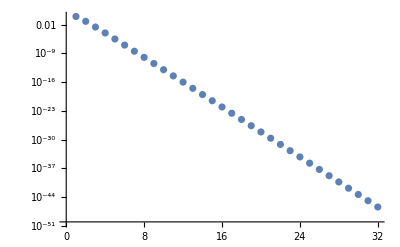

```mathematica
ListLogPlot[evs]
```

```mathematica
fit[n_]=Exp[Fit[Log[evs],{1,n},n]]/.Exp[a_+b_]:>Exp[N[a]]Exp[N[b]]
```

106.542 ⅇ^(-3.47456 n)

The model is a reasonable predictor of magnitude for larger values of n:

```mathematica
RealExponent[fit[100]]
```

-148.871

```mathematica
RealExponent[Eigenvalues[HilbertMatrix[10,WorkingPrecision->200],-1]]
```

{-12.9613}

The condition number increases exponentially with n:

```mathematica
capprox[n_]=2/(79.9534307952165 ⅇ^(-3.4421139525803413 n))
```

0.0250146 ⅇ^(3.44211 n)

The 2-norm condition number is the ratio of largest to smallest eigenvalue due to symmetry:

```mathematica
cnos=Table[Apply[Divide,Eigenvalues[HilbertMatrix[n,WorkingPrecision->2n+20]][[{1,-1}]]],{n,32}];
```

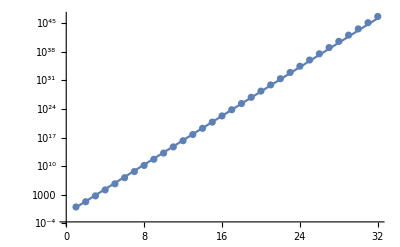

```mathematica
Show[ListLogPlot[cnos],LogPlot[capprox[n],{n,1,32}]]
```